# Power Potential

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=(λ*x^2)/k^2
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1=1

```mathematica
Solve[ε1==1,x]
```

{{x→-(√2 √a)/k},{x→(√2 √a)/k}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=(√2 √a)/k// Simplify;
```

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[-(k^2/a)*(v[x]/v'[x]),x]
```

-(k^2 x^2)/(4 a)

```mathematica
Solve[-(k^2 *xf^2)/(4*a)+(k^2 *x^2)/(4*a)==Y,x]
```

{{x→-(√2 √(a+2 a Y))/k},{x→(√2 √(a+2 a Y))/k}}

```mathematica
xi=(√2 √(a+2 a Y))/k// Simplify;
```

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi and we take the Taylor approximation for N → ∞. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
ε1i=ε1 /. x->xi// Simplify;
ε2i=ε2 /. x->xi// Simplify;
εi=ε /. x->xi// Simplify;
η1i=η1 /. x->xi// Simplify;
ηi=η/. x->xi// Simplify;
```

The primordial density perturbation and the tensor to scalar ratio is given as:

```mathematica
ns=1-6*ε1+2*η1// Simplify;
nsi=ns/. x->xi// Simplify;
```

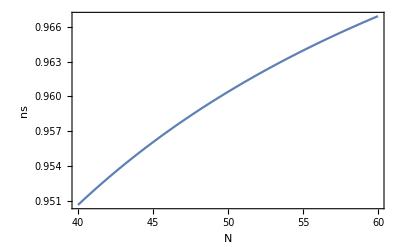

```mathematica
Plot[nsi,{Y,40,60},Frame->True,FrameLabel->{"N","ns"}]
```

```mathematica
Reduce[0.9691>nsi>0.9607,Y]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

50.3906<Y<64.2249

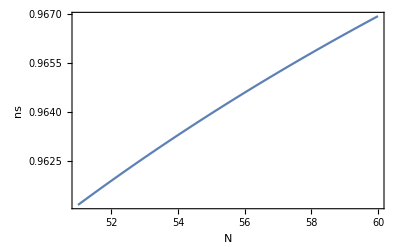

```mathematica
Plot[nsi,{Y,51,60},Frame->True,FrameLabel->{"N","ns"}]
```

```mathematica
r=16*ε1i// Simplify
```

16/(1+2 Y)

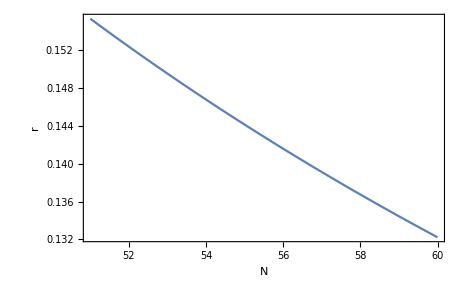

```mathematica
Plot[r,{Y,51,60},Frame->True,FrameLabel->{"N","r"}]
```

The plots for the slow-roll parameters

```mathematica
Plot[{ε1i,ε2i,εi},{Y,51,60},Frame->True,FrameLabel->{"N","Slow-roll indices arithmetic values"},PlotLabels->Automatic]
Plot[{η1i,ηi},{Y,51,60},Frame->True,FrameLabel->{"N","Slow-roll indices arithmetic values"},PlotLabels->Automatic]
```

-Graphics-

-Graphics-

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

1/(√(a (1/2+Y)))

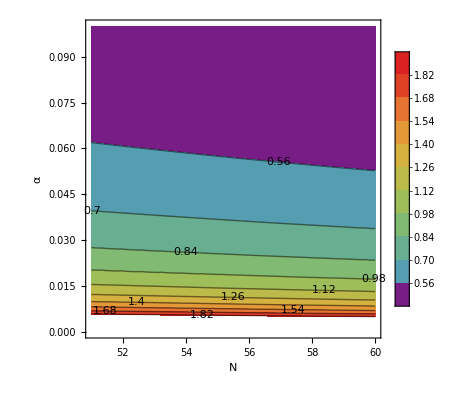

```mathematica
s=v'[x]/v[x]// Simplify;
sinitial=s/. x->xi// Simplify;
sinitialk=sinitial/. k->1// Simplify
ContourPlot[sinitialk,{Y,51,60},{a,0,0.1},ContourLabels->True,FrameLabel->{"N","α"},ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

-1/(a+2 a Y)

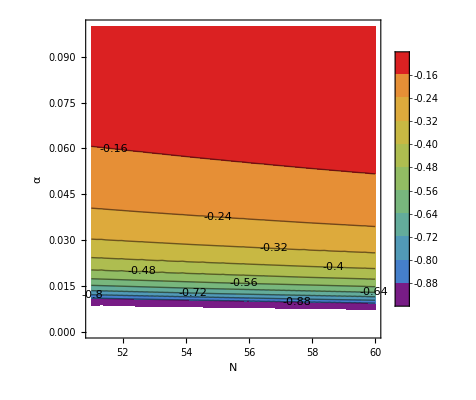

```mathematica
s1=-v''[x]/v[x];
sinitial1=s1/. x->xi// Simplify;
sinitialk1=sinitial1/. k->1//Simplify
ContourPlot[sinitialk1,{Y,51,60},{a,0,0.1},ContourLabels->True,FrameLabel->{"N","α"},ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

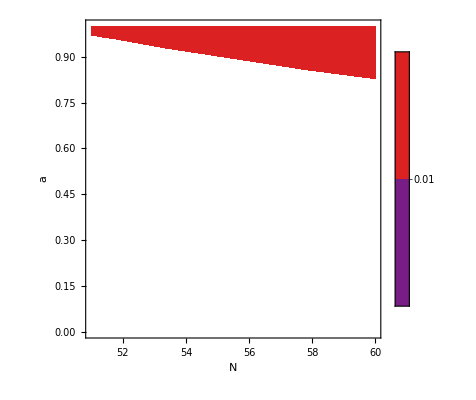

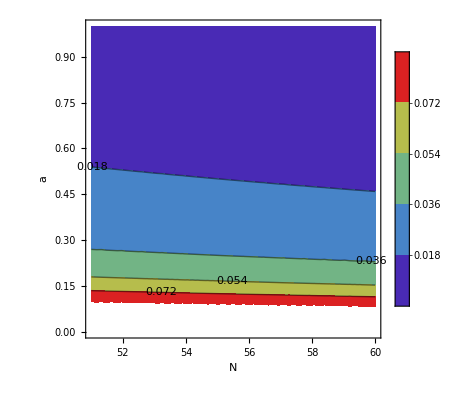

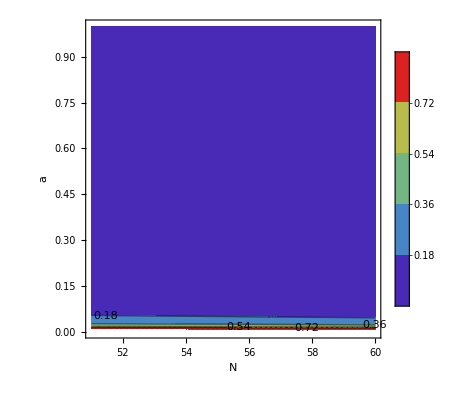

```mathematica
ContourPlot[εi,{Y,51,60},{a,0,1},ContourLabels->True,FrameLabel->{"N","a"},ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10,PlotRange->{-0.01,0.01}]
ContourPlot[εi,{Y,51,60},{a,0,1},ContourLabels->True,FrameLabel->{"N","a"},ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10,PlotRange->{-0.1,0.1}]
ContourPlot[εi,{Y,51,60},{a,0,1},ContourLabels->True,FrameLabel->{"N","a"},ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10,PlotRange->{-0.99,0.99}]
```